SetDelayed::write: Tag If in If[√(x^2+y^2)>1/10000000000000000,(HeavisideTheta[thickness^2/4-Plus[«3»]^2]-HeavisideTheta[Power[«2»] Power[«2»]-Power[«2»]])/(2 thickness √(x^2+y^2)),0.][x_,y_] is Protected.

1.04625

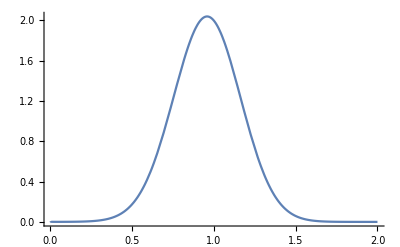

-Graphics3D-

-Graphics3D-

```mathematica
m=1;
s=0.2;
psir=Exp[-(r-m)^2/(2 s^2)]/(r s √(2 π));
dpsir=D[psir,r];
psi[x_,y_]:=psir/.r->√(x^2+y^2);
dpsi[x_,y_]:=dpsir/.r->√(x^2+y^2);
a=1;
pr=2a;
NIntegrate[a^-1*psir/.{r->a^-1*t},{t,10^-3,a+pr}]
Plot[a^-1*psir/.{r->a^-1*t},{t,10^-3,pr},PlotRange->All]
Plot3D[a^-1*psi[a^-1 x,a^-1 y],{x,-pr,pr},{y,-pr,pr},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->50]
Plot3D[a^-1 dpsi[a^-1 x,a^-1 y],{x,-pr,pr},{y,-pr,pr},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->50]
```

0.

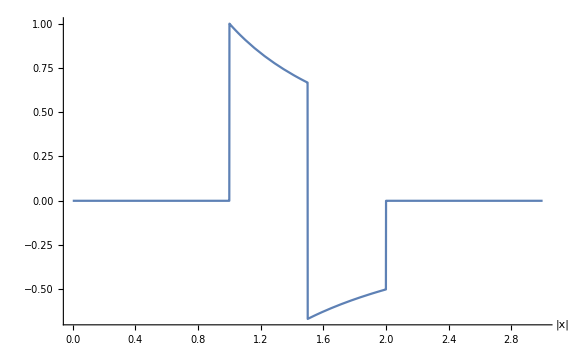

wavelet.png

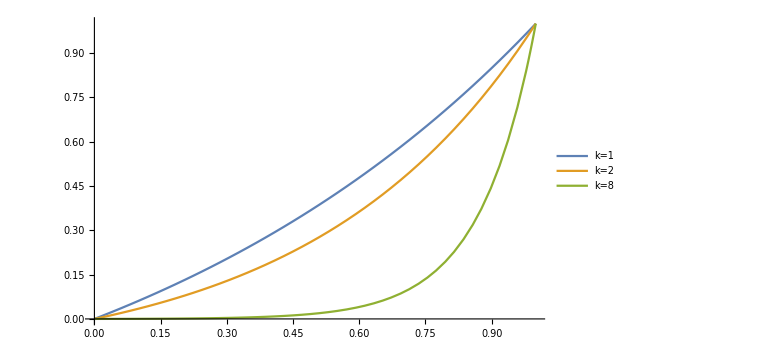

filtering-fn.png

-Graphics3D-

```mathematica
radius=1.5;
thickness=1.0;
psir=If[r>10^-16,If[radius-thickness/2<=r<radius,1,If[radius+thickness/2>=r>radius,-1,0]]/(thickness*r)(*(HeavisideTheta[thickness^2/4-(r-radius+thickness/2)^2]-HeavisideTheta[thickness^2/4-(r-radius-thickness/2)^2])/(2thickness*r)*),0.0];
psi=psir/.r->√(x^2+y^2);
scale=(Exp[k x]-1)/(Exp[k]-1);
pr=1;
Integrate[psir*r,{r,radius-thickness/2,radius+thickness/2}]
Plot[psir,{r,radius-thickness/2-pr,radius+thickness/2+pr},AxesLabel->{"|x|"},PlotRange->All,ImageSize->Large]
Export["wavelet.png",%]
Plot[{scale/.{k->1},scale/.{k->2},scale/.{k->8}},{x,0,1},PlotRange->{{0,1},{0,Automatic}},PlotLegends->{"k=1","k=2","k=8"},ImageSize->Large]
Export["filtering-fn.png",%]
RevolutionPlot3D[psir,{r,radius-thickness/2-pr,radius+thickness/2+pr},ColorFunction->"TemperatureMap",PlotRange->All,PlotPoints->50]
```

```mathematica
img=Image[Graphics[{{EdgeForm[{Thickness[0.03],Black}],White,Rectangle[{2,1}]},{EdgeForm[{Thickness[0.03],Black}],White,Triangle[{{2,2.8},{2,3.8},{3,2.8}}]},{Thickness[0.03],Black,Circle[{2,2},0.4]},{Thickness[0.03],Black,Circle[{4,2.2},0.8]}},ImageSize->200]]
f=Map[1.0-Total[#]/N[255*3]&,ImageData[img,"Byte"],{2}];
```

-Graphics-

```mathematica
img=Image[Graphics[{{Black,Rectangle[{2,1}]},{Black,Triangle[{{2,2.8},{2,3.8},{3,2.8}}]},{Black,Disk[{3.2,3.4},0.3]},{Black,Disk[{2,2},0.4]},{Black,Disk[{4,2.2},0.8]}},ImageSize->200]]
Export["f.png",%]
f=Map[1.0-Total[#]/N[255*3]&,ImageData[img,"Byte"],{2}];
```

-Graphics-

f.png

```mathematica
SetDirectory[NotebookDirectory[]];
Export["f.tsv",f, "Table"]
```

f.tsv

```mathematica
rs=First@Import["r.ssv","Table"];
rbeg=First@rs;rend=Last@rs; rstep=rs⟦2⟧-rbeg; 
rtoi[r_]:=(r-rbeg)/rstep+1;
wfs=SequenceSplit[Import["wfs.ssv","Table"],{{}}];
wwfs=SequenceSplit[Import["wwfs.ssv","Table"],{{}}];
```

```mathematica
(*nwfs=Map[
With[{min=Min@Flatten@#,diff=Max@Flatten@#-Min@Flatten@#},Map[1.0-(#-min)/diff&,#,{2}]]&,
wfs];
nwwfs=Map[
With[{min=Min@Flatten@#,diff=Max@Flatten@#-Min@Flatten@#},Map[1.0-(#-min)/diff&,#,{2}]]&,
wwfs];
wimgs=Map[Image@#&,nwfs];
wwimgs=Map[Image@#&,nwwfs];
Manipulate[{wimgs⟦rtoi[r]⟧,wwimgs⟦rtoi[r]⟧},{r,rbeg,rend,rstep}]*)
nwfs=Map[
With[{max=1(*Max@Abs@Flatten@#*)},Map[#/(2.0)+0.5&,#,{2}]]&,
wfs];
nwwfs=Map[
With[{max=1(*Max@Abs@Flatten@#*)},Map[#/(2.0)+0.5&,#,{2}]]&,
wwfs];
fieldPlot[field_]:=ArrayPlot[field,ColorFunction->(ColorData["GrayTones"][#]&),ColorFunctionScaling->False];
fieldPlots[field_]:=Map[fieldPlot[#]&,field];
wplots=fieldPlots[nwfs];
wwplots=fieldPlots[nwwfs];
Manipulate[{wplots⟦rtoi[r]⟧,wwplots⟦rtoi[r]⟧},{r,rbeg,rend,rstep}]
```

```mathematica
Export["nwf,r=24.png",fieldPlot[nwfs⟦rtoi[24]⟧]]
Export["nwwf,r=24.png",fieldPlot[nwwfs⟦rtoi[24]⟧]]
```

nwf,r=24.png

nwwf,r=24.png

```mathematica
nwfs⟦rtoi[12],100,100⟧
```

0.499882

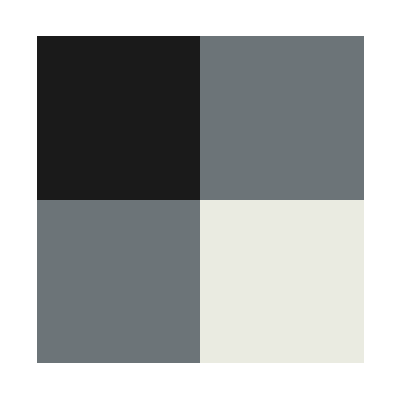

```mathematica
ArrayPlot[{{0.0,0.5},{0.5,1.0}},ColorFunction->(ColorData["GrayTones"][#]&),ColorFunctionScaling->False]
```

```mathematica
Max[Flatten@wfs]
```

1.17797×10^11

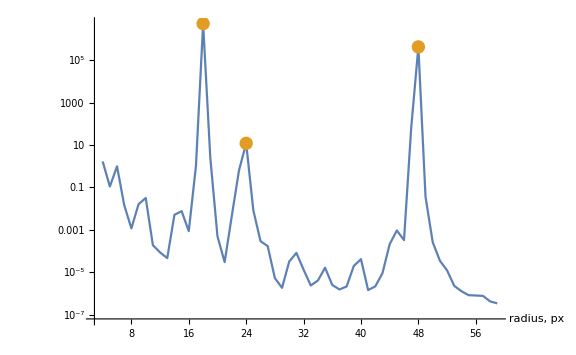

intensity-radius,thickness=4.png

```mathematica
intnwfs=MapThread[{#1,Total[Abs@Flatten@#2]/Length@Flatten@#2}&,{rs,wfs}];
cirpts={intnwfs⟦rtoi[18]⟧,intnwfs⟦rtoi[24]⟧,intnwfs⟦rtoi[48]⟧};
ListLinePlot[{intnwfs,cirpts},Joined->{True,False},PlotRange->All,ScalingFunctions->"Log",AxesLabel->{"radius, px"},ImageSize->Large]
Export["intensity-radius,thickness=4.png",%]
```

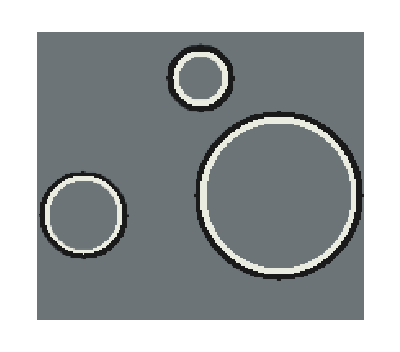

nwwf,combination.png

```mathematica
combineFields[radiuses_]:=Plus@@Map[nwwfs⟦rtoi[#]⟧-0.5&,radiuses]+0.5;
fieldPlot[combineFields[{17,24,48}]]
Export["nwwf,combination.png",%]
```

```mathematica
cnwwfss=Table[Map[If[Abs[#-0.5]<t,0.5,#]&,nwwfs,{3}],{t,0.0,0.5,0.05}];
cwwimgss=Map[fieldPlots@#&,cnwwfss];
Manipulate[cwwimgss⟦t,rtoi[r]⟧,{t,1,Length@cwwimgss,1},{r,rbeg,rend,rstep}]
```

ArrayPlot::mat: Argument {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,«16»,0.500018,0.500082,0.500103,0.500097,0.500064,0.500028,0.500007,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,«150»} at position 1 is not a list of lists.

ArrayPlot::mat: Argument {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,«18»,0.500015,0.500094,0.500114,0.500103,0.500066,0.500028,0.500007,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,«150»} at position 1 is not a list of lists.

ArrayPlot::mat: Argument {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,«19»,0.499598,0.500033,0.500106,0.50012,0.500105,0.500066,0.500028,0.500007,0.5,0.5,0.5,0.5,0.5,0.5,0.5,«150»} at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted